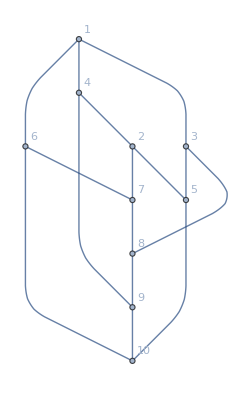

```mathematica
g=Graph[EdgeList[GraphData["PetersenGraph"]],VertexLabels->"Name" ,GraphLayout->"LayeredDigraphEmbedding"]
```

```mathematica
ToLogical[g_,max_:4]:=Block[{exp,vertex,vertices,var,var1,var2,edges,edgeIndex,edge},exp=True;
vertices=VertexList[g];
For[vertex=1,vertex≤Length[vertices],vertex++,var=Symbol["x"<>ToString[vertices[[vertex]]]];
exp=exp&&Element[var,Integers];];
For[vertex=1,vertex≤Length[vertices],vertex++,var=Symbol["x"<>ToString[vertices[[vertex]]]];
exp=exp&&(1≤var≤max);];
edges=EdgeList[g];
For[edgeIndex=1,edgeIndex≤Length[edges],edgeIndex++,edge=edges[[edgeIndex]];
var1=Symbol["x"<>ToString[edge[[1]]]];
var2=Symbol["x"<>ToString[edge[[2]]]];
exp=exp&&var1≠var2;];
exp]
```

```mathematica
exp=ToLogical[g,5]
```

x1∈Integers&&x3∈Integers&&x4∈Integers&&x6∈Integers&&x2∈Integers&&x5∈Integers&&x7∈Integers&&x8∈Integers&&x9∈Integers&&x10∈Integers&&1≤x1≤5&&1≤x3≤5&&1≤x4≤5&&1≤x6≤5&&1≤x2≤5&&1≤x5≤5&&1≤x7≤5&&1≤x8≤5&&1≤x9≤5&&1≤x10≤5&&x1≠x3&&x1≠x4&&x1≠x6&&x2≠x4&&x2≠x5&&x2≠x7&&x3≠x5&&x3≠x8&&x4≠x9&&x5≠x10&&x6≠x7&&x6≠x10&&x7≠x8&&x8≠x9&&x9≠x10

```mathematica
36281*120
```

4353720

```mathematica
EdgeCount[g]
```

15

```mathematica
(CompleteBaseCoeff[ ChromaticPolynomial[g,x]]//Rest)
```

{0,0,20,520,2244,2865,1435,315,30,1}

```mathematica
N[22*24/694337290,50]
```

7.604373373061959555708148701044127991454988684246×10^-7

```mathematica
Table[StirlingS2[17,k],{k,1,17}]
```

{1,65535,21457825,694337290,5652751651,17505749898,25708104786,20415995028,9528822303,2758334150,512060978,62022324,4910178,249900,7820,136,1}

```mathematica
CompleteBaseCoeff[ ChromaticPolynomial[g,x]]
```

{0,0,0,20,520,2244,2865,1435,315,30,1}

```mathematica
ChromaticPolynomial[g,4]
```

12960

```mathematica
CompleteBaseCoeff[ ChromaticPolynomial[g2,x]]
```

{ChromaticPolynomial[g2,x]}

```mathematica
528/24
```

22

```mathematica
sols=ToVarsLogical[g,True]
```

{{x1→1,x3→2,x4→2,x6→2,x2→1,x5→3,x7→3,x8→1,x9→3,x10→1},{x1→1,x3→2,x4→2,x6→2,x2→1,x5→3,x7→3,x8→1,x9→3,x10→4},{x1→1,x3→2,x4→2,x6→2,x2→1,x5→3,x7→3,x8→1,x9→4,x10→1},{x1→1,x3→2,x4→2,x6→2,x2→1,x5→3,x7→3,x8→4,x9→1,x10→4},{x1→1,x3→2,x4→2,x6→2,x2→1,x5→3,x7→3,x8→4,x9→3,x10→1},12951,{x1→4,x3→3,x4→3,x6→3,x2→4,x5→2,x7→2,x8→1,x9→4,x10→1},{x1→4,x3→3,x4→3,x6→3,x2→4,x5→2,x7→2,x8→4,x9→1,x10→4},{x1→4,x3→3,x4→3,x6→3,x2→4,x5→2,x7→2,x8→4,x9→2,x10→1},{x1→4,x3→3,x4→3,x6→3,x2→4,x5→2,x7→2,x8→4,x9→2,x10→4}}
 |  |  |  |

```mathematica
Length[sols]
```

12960

```mathematica
SolutionToPartition[ol_]:=Block[{assoc=Association[],i,val},
For[i=1,i≤4,i++,
assoc[i]={}
];
For[i=1,i≤Length[ol],i++,
val=ol[[i,2]];
assoc[val]=Append[assoc[val], IntegerString[i,10,2]]
];
Row[Riffle[Sort[Select[Table[StringRiffle[assoc[key],"-"],{key,Keys[assoc]}],#≠""&]],Style["|",Red]]]
]
```

```mathematica
SolutionToPartition[ol_,vertices_]:=Block[{assoc=Association[],i,val},
For[i=1,i≤4,i++,
assoc[i]={}
];
Table[val=ol[[i,2]];
assoc[val]=Append[assoc[val], IntegerString[i,10,2]]
,{i,vertices}];
Row[Riffle[Sort[Select[Table[StringRiffle[assoc[key],"-"],{key,Keys[assoc]}],#≠""&]],Style["|",Red]]]
]
```

```mathematica
SolutionToPartition[{x1->1,x2->2,x3->3,x4->2,x5->3,x6->4,x7->1,x8->4,x9->2,x10->1,x11->3,x12->1,x13->2,x14->4,x15->3,x16->4,x17->2}]
```

01-07-10-12|02-04-09-13-17|03-05-11-15|06-08-14-16

```mathematica
Map[First,Map[SolutionToPartition[#]&,sols]//Sort//Tally]//Length
```

540

```mathematica
TableForm[Map[First,Map[SolutionToPartition[#,{1,4,9,10,6}]&,sols]//Sort//Tally]]
```

01-10|04-09-06
01|04-09-06|10
01-06|04-09|10
01-09|04-06|10
01-09-06|04|10
01-10|04|09-06
01-10|04-06|09
01-10|04-09|06
01|04|09-06|10
01|04-06|09|10
01|04-09|06|10
01-06|04|09|10
01-09|04|06|10
01-10|04|06|09

```mathematica
TableForm[Map[First,Map[SolutionToPartition[#]&,sols]//Sort//Tally]]
```

01-05-08|02-03-07-10|04-06-09
01-05-08-10|02-03-04|06-07-09
01-05-08-10|02-03-07|04-06-09
01-05-08-10|02-04-09|03-06-07
01-05-08-10|02-07-09|03-04-06
01-05-09|02-03-07-10|04-06-08
01-05-09|02-07-10|03-04-06-08
01-05-10|02-07-09|03-04-06-08
01-06-07|02-04-05-09|03-08-10
01-06-07-09|02-03-04|05-08-10
01-06-07-09|02-03-10|04-05-08
01-06-07-09|02-04-05|03-08-10
01-06-07-09|02-05-10|03-04-08
01-06-08|02-03-07-10|04-05-09
01-06-08|02-04-05-09|03-07-10
01-06-09|02-03-07-10|04-05-08
01-07-09|02-05-10|03-04-06-08
01-07-10|02-04-05-09|03-06-08
01-07-10|02-05-09|03-04-06-08
01-08-10|02-04-05-09|03-06-07
01|02-03-04|05-08-10|06-07-09
01|02-03-07|04-06-09|05-08-10
01|02-03-07-10|04-05-08|06-09
01|02-03-07-10|04-05-09|06-08
01|02-03-07-10|04-06-08|05-09
01|02-03-07-10|04-06-09|05-08
01|02-03-10|04-05-08|06-07-09
01|02-04-05|03-08-10|06-07-09
01|02-04-05-09|03-06-07|08-10
01|02-04-05-09|03-06-08|07-10
01|02-04-05-09|03-07-10|06-08
01|02-04-05-09|03-08-10|06-07
01|02-04-09|03-06-07|05-08-10
01|02-05-09|03-04-06-08|07-10
01|02-05-09|03-07-10|04-06-08
01|02-05-10|03-04-06-08|07-09
01|02-05-10|03-04-08|06-07-09
01|02-07-09|03-04-06|05-08-10
01|02-07-09|03-04-06-08|05-10
01|02-07-10|03-04-06-08|05-09
01|02-07-10|03-06-08|04-05-09
01-05|02-03-04|06-07-09|08-10
01-05|02-03-07|04-06-09|08-10
01-05|02-03-07-10|04-06-08|09
01-05|02-03-07-10|04-06-09|08
01-05|02-03-07-10|04-08|06-09
01-05|02-03-07-10|04-09|06-08
01-05|02-03-10|04-06-08|07-09
01-05|02-03-10|04-08|06-07-09
01-05|02-04|03-08-10|06-07-09
01-05|02-04-09|03-06-07|08-10
01-05|02-04-09|03-06-08|07-10
01-05|02-04-09|03-07-10|06-08
01-05|02-04-09|03-08-10|06-07
01-05|02-07|03-08-10|04-06-09
01-05|02-07-09|03-04-06|08-10
01-05|02-07-09|03-04-06-08|10
01-05|02-07-09|03-08-10|04-06
01-05|02-07-09|03-10|04-06-08
01-05|02-07-10|03-04-06-08|09
01-05|02-07-10|03-04-08|06-09
01-05|02-07-10|03-06-08|04-09
01-05|02-07-10|03-08|04-06-09
01-05|02-09|03-04-06-08|07-10
01-05|02-09|03-07-10|04-06-08
01-05|02-10|03-04-06-08|07-09
01-05|02-10|03-04-08|06-07-09
01-05-08|02|03-07-10|04-06-09
01-05-08|02-03|04-06-09|07-10
01-05-08|02-03-04|06-07-09|10
01-05-08|02-03-04|06-09|07-10
01-05-08|02-03-07|04-06-09|10
01-05-08|02-03-07-10|04|06-09
01-05-08|02-03-07-10|04-06|09
01-05-08|02-03-07-10|04-09|06
01-05-08|02-03-10|04|06-07-09
01-05-08|02-03-10|04-06|07-09
01-05-08|02-03-10|04-06-09|07
01-05-08|02-03-10|04-09|06-07
01-05-08|02-04|03-07-10|06-09
01-05-08|02-04|03-10|06-07-09
01-05-08|02-04-09|03-06|07-10
01-05-08|02-04-09|03-06-07|10
01-05-08|02-04-09|03-07-10|06
01-05-08|02-04-09|03-10|06-07
01-05-08|02-07|03-10|04-06-09
01-05-08|02-07-09|03-04-06|10
01-05-08|02-07-09|03-10|04-06
01-05-08|02-07-10|03|04-06-09
01-05-08|02-07-10|03-04|06-09
01-05-08|02-07-10|03-04-06|09
01-05-08|02-07-10|03-06|04-09
01-05-08|02-09|03-04-06|07-10
01-05-08|02-09|03-07-10|04-06
01-05-08|02-10|03-04|06-07-09
01-05-08|02-10|03-04-06|07-09
01-05-08|02-10|03-06-07|04-09
01-05-08|02-10|03-07|04-06-09
01-05-08-10|02|03-04|06-07-09
01-05-08-10|02|03-04-06|07-09
01-05-08-10|02|03-06-07|04-09
01-05-08-10|02|03-07|04-06-09
01-05-08-10|02-03|04|06-07-09
01-05-08-10|02-03|04-06|07-09
01-05-08-10|02-03|04-06-09|07
01-05-08-10|02-03|04-09|06-07
01-05-08-10|02-03-04|06|07-09
01-05-08-10|02-03-04|06-07|09
01-05-08-10|02-03-04|06-09|07
01-05-08-10|02-03-07|04|06-09
01-05-08-10|02-03-07|04-06|09
01-05-08-10|02-03-07|04-09|06
01-05-08-10|02-04|03|06-07-09
01-05-08-10|02-04|03-06|07-09
01-05-08-10|02-04|03-06-07|09
01-05-08-10|02-04|03-07|06-09
01-05-08-10|02-04-09|03|06-07
01-05-08-10|02-04-09|03-06|07
01-05-08-10|02-04-09|03-07|06
01-05-08-10|02-07|03|04-06-09
01-05-08-10|02-07|03-04|06-09
01-05-08-10|02-07|03-04-06|09
01-05-08-10|02-07|03-06|04-09
01-05-08-10|02-07-09|03|04-06
01-05-08-10|02-07-09|03-04|06
01-05-08-10|02-07-09|03-06|04
01-05-08-10|02-09|03-04|06-07
01-05-08-10|02-09|03-04-06|07
01-05-08-10|02-09|03-06-07|04
01-05-08-10|02-09|03-07|04-06
01-05-09|02|03-04-06-08|07-10
01-05-09|02|03-07-10|04-06-08
01-05-09|02-03|04-06-08|07-10
01-05-09|02-03-04|06-07|08-10
01-05-09|02-03-04|06-08|07-10
01-05-09|02-03-07|04-06|08-10
01-05-09|02-03-07|04-06-08|10
01-05-09|02-03-07-10|04|06-08
01-05-09|02-03-07-10|04-06|08
01-05-09|02-03-07-10|04-08|06
01-05-09|02-03-10|04-06-08|07
01-05-09|02-03-10|04-08|06-07
01-05-09|02-04|03-06-07|08-10
01-05-09|02-04|03-06-08|07-10
01-05-09|02-04|03-07-10|06-08
01-05-09|02-04|03-08-10|06-07
01-05-09|02-07|03-04-06|08-10
01-05-09|02-07|03-04-06-08|10
01-05-09|02-07|03-08-10|04-06
01-05-09|02-07|03-10|04-06-08
01-05-09|02-07-10|03|04-06-08
01-05-09|02-07-10|03-04|06-08
01-05-09|02-07-10|03-04-06|08
01-05-09|02-07-10|03-04-08|06
01-05-09|02-07-10|03-06|04-08
01-05-09|02-07-10|03-06-08|04
01-05-09|02-07-10|03-08|04-06
01-05-09|02-10|03-04-06-08|07
01-05-09|02-10|03-04-08|06-07
01-05-09|02-10|03-06-07|04-08
01-05-09|02-10|03-07|04-06-08
01-05-10|02|03-04-06-08|07-09
01-05-10|02|03-04-08|06-07-09
01-05-10|02-03|04-06-08|07-09
01-05-10|02-03|04-08|06-07-09
01-05-10|02-03-04|06-07-09|08
01-05-10|02-03-04|06-08|07-09
01-05-10|02-03-07|04-06-08|09
01-05-10|02-03-07|04-06-09|08
01-05-10|02-03-07|04-08|06-09
01-05-10|02-03-07|04-09|06-08
01-05-10|02-04|03-06-08|07-09
01-05-10|02-04|03-08|06-07-09
01-05-10|02-04-09|03-06-07|08
01-05-10|02-04-09|03-06-08|07
01-05-10|02-04-09|03-07|06-08
01-05-10|02-04-09|03-08|06-07
01-05-10|02-07|03-04-06-08|09
01-05-10|02-07|03-04-08|06-09
01-05-10|02-07|03-06-08|04-09
01-05-10|02-07|03-08|04-06-09
01-05-10|02-07-09|03|04-06-08
01-05-10|02-07-09|03-04|06-08
01-05-10|02-07-09|03-04-06|08
01-05-10|02-07-09|03-04-08|06
01-05-10|02-07-09|03-06|04-08
01-05-10|02-07-09|03-06-08|04
01-05-10|02-07-09|03-08|04-06
01-05-10|02-09|03-04-06-08|07
01-05-10|02-09|03-04-08|06-07
01-05-10|02-09|03-06-07|04-08
01-05-10|02-09|03-07|04-06-08
01-06|02-03-04|05-08-10|07-09
01-06|02-03-07|04-05-09|08-10
01-06|02-03-07|04-09|05-08-10
01-06|02-03-07-10|04-05-08|09
01-06|02-03-07-10|04-05-09|08
01-06|02-03-07-10|04-08|05-09
01-06|02-03-07-10|04-09|05-08
01-06|02-03-10|04-05-08|07-09
01-06|02-04-05|03-08-10|07-09
01-06|02-04-05-09|03-07|08-10
01-06|02-04-05-09|03-07-10|08
01-06|02-04-05-09|03-08|07-10
01-06|02-04-05-09|03-08-10|07
01-06|02-04-09|03-07|05-08-10
01-06|02-04-09|03-07-10|05-08
01-06|02-05-09|03-04-08|07-10
01-06|02-05-09|03-07-10|04-08
01-06|02-05-10|03-04-08|07-09
01-06|02-07|03-08-10|04-05-09
01-06|02-07-09|03-04|05-08-10
01-06|02-07-09|03-04-08|05-10
01-06|02-07-09|03-08-10|04-05
01-06|02-07-09|03-10|04-05-08
01-06|02-07-10|03-04-08|05-09
01-06|02-07-10|03-08|04-05-09
01-06|02-09|03-07-10|04-05-08
01-06-07|02|03-08-10|04-05-09
01-06-07|02-03|04-05-09|08-10
01-06-07|02-03|04-09|05-08-10
01-06-07|02-03-04|05-08-10|09
01-06-07|02-03-04|05-09|08-10
01-06-07|02-03-10|04-05-08|09
01-06-07|02-03-10|04-05-09|08
01-06-07|02-03-10|04-08|05-09
01-06-07|02-03-10|04-09|05-08
01-06-07|02-04|03-08-10|05-09
01-06-07|02-04-05|03-08-10|09
01-06-07|02-04-05-09|03|08-10
01-06-07|02-04-05-09|03-08|10
01-06-07|02-04-05-09|03-10|08
01-06-07|02-04-09|03|05-08-10
01-06-07|02-04-09|03-08|05-10
01-06-07|02-04-09|03-08-10|05
01-06-07|02-04-09|03-10|05-08
01-06-07|02-05|03-08-10|04-09
01-06-07|02-05-09|03-04|08-10
01-06-07|02-05-09|03-04-08|10
01-06-07|02-05-09|03-08-10|04
01-06-07|02-05-09|03-10|04-08
01-06-07|02-05-10|03-04-08|09
01-06-07|02-05-10|03-08|04-09
01-06-07|02-09|03-04|05-08-10
01-06-07|02-09|03-04-08|05-10
01-06-07|02-09|03-08-10|04-05
01-06-07|02-09|03-10|04-05-08
01-06-07|02-10|03-04-08|05-09
01-06-07|02-10|03-08|04-05-09
01-06-07-09|02|03-04|05-08-10
01-06-07-09|02|03-04-08|05-10
01-06-07-09|02|03-08-10|04-05
01-06-07-09|02|03-10|04-05-08
01-06-07-09|02-03|04|05-08-10
01-06-07-09|02-03|04-05|08-10
01-06-07-09|02-03|04-05-08|10
01-06-07-09|02-03|04-08|05-10
01-06-07-09|02-03-04|05|08-10
01-06-07-09|02-03-04|05-08|10
01-06-07-09|02-03-04|05-10|08
01-06-07-09|02-03-10|04|05-08
01-06-07-09|02-03-10|04-05|08
01-06-07-09|02-03-10|04-08|05
01-06-07-09|02-04|03|05-08-10
01-06-07-09|02-04|03-08|05-10
01-06-07-09|02-04|03-08-10|05
01-06-07-09|02-04|03-10|05-08
01-06-07-09|02-04-05|03|08-10
01-06-07-09|02-04-05|03-08|10
01-06-07-09|02-04-05|03-10|08
01-06-07-09|02-05|03-04|08-10
01-06-07-09|02-05|03-04-08|10
01-06-07-09|02-05|03-08-10|04
01-06-07-09|02-05|03-10|04-08
01-06-07-09|02-05-10|03|04-08
01-06-07-09|02-05-10|03-04|08
01-06-07-09|02-05-10|03-08|04
01-06-07-09|02-10|03|04-05-08
01-06-07-09|02-10|03-04|05-08
01-06-07-09|02-10|03-04-08|05
01-06-07-09|02-10|03-08|04-05
01-06-08|02|03-07-10|04-05-09
01-06-08|02-03|04-05-09|07-10
01-06-08|02-03-04|05-09|07-10
01-06-08|02-03-04|05-10|07-09
01-06-08|02-03-07|04-05-09|10
01-06-08|02-03-07|04-09|05-10
01-06-08|02-03-07-10|04|05-09
01-06-08|02-03-07-10|04-05|09
01-06-08|02-03-07-10|04-09|05
01-06-08|02-03-10|04-05|07-09
01-06-08|02-03-10|04-05-09|07
01-06-08|02-04|03-07-10|05-09
01-06-08|02-04-05|03-07-10|09
01-06-08|02-04-05|03-10|07-09
01-06-08|02-04-05-09|03|07-10
01-06-08|02-04-05-09|03-07|10
01-06-08|02-04-05-09|03-10|07
01-06-08|02-04-09|03-07|05-10
01-06-08|02-04-09|03-07-10|05
01-06-08|02-05|03-07-10|04-09
01-06-08|02-05-09|03-04|07-10
01-06-08|02-05-09|03-07-10|04
01-06-08|02-05-10|03-04|07-09
01-06-08|02-05-10|03-07|04-09
01-06-08|02-07|03-10|04-05-09
01-06-08|02-07-09|03-04|05-10
01-06-08|02-07-09|03-10|04-05
01-06-08|02-07-10|03|04-05-09
01-06-08|02-07-10|03-04|05-09
01-06-08|02-09|03-07-10|04-05
01-06-08|02-10|03-07|04-05-09
01-06-09|02|03-07-10|04-05-08
01-06-09|02-03|04-05-08|07-10
01-06-09|02-03-04|05-08|07-10
01-06-09|02-03-04|05-08-10|07
01-06-09|02-03-07|04|05-08-10
01-06-09|02-03-07|04-05|08-10
01-06-09|02-03-07|04-05-08|10
01-06-09|02-03-07|04-08|05-10
01-06-09|02-03-07-10|04|05-08
01-06-09|02-03-07-10|04-05|08
01-06-09|02-03-07-10|04-08|05
01-06-09|02-03-10|04-05-08|07
01-06-09|02-04|03-07|05-08-10
01-06-09|02-04|03-07-10|05-08
01-06-09|02-04-05|03-07|08-10
01-06-09|02-04-05|03-07-10|08
01-06-09|02-04-05|03-08|07-10
01-06-09|02-04-05|03-08-10|07
01-06-09|02-05|03-04-08|07-10
01-06-09|02-05|03-07-10|04-08
01-06-09|02-05-10|03-04-08|07
01-06-09|02-05-10|03-07|04-08
01-06-09|02-07|03-04|05-08-10
01-06-09|02-07|03-04-08|05-10
01-06-09|02-07|03-08-10|04-05
01-06-09|02-07|03-10|04-05-08
01-06-09|02-07-10|03|04-05-08
01-06-09|02-07-10|03-04|05-08
01-06-09|02-07-10|03-04-08|05
01-06-09|02-07-10|03-08|04-05
01-06-09|02-10|03-07|04-05-08
01-07|02-03|04-06-09|05-08-10
01-07|02-03-04|05-08-10|06-09
01-07|02-03-10|04-05-08|06-09
01-07|02-03-10|04-05-09|06-08
01-07|02-03-10|04-06-08|05-09
01-07|02-03-10|04-06-09|05-08
01-07|02-04-05|03-08-10|06-09
01-07|02-04-05-09|03-06|08-10
01-07|02-04-05-09|03-06-08|10
01-07|02-04-05-09|03-08-10|06
01-07|02-04-05-09|03-10|06-08
01-07|02-04-09|03-06|05-08-10
01-07|02-04-09|03-06-08|05-10
01-07|02-05|03-08-10|04-06-09
01-07|02-05-09|03-04-06|08-10
01-07|02-05-09|03-04-06-08|10
01-07|02-05-09|03-08-10|04-06
01-07|02-05-09|03-10|04-06-08
01-07|02-05-10|03-04-06-08|09
01-07|02-05-10|03-04-08|06-09
01-07|02-05-10|03-06-08|04-09
01-07|02-05-10|03-08|04-06-09
01-07|02-09|03-04-06|05-08-10
01-07|02-09|03-04-06-08|05-10
01-07|02-10|03-04-06-08|05-09
01-07|02-10|03-06-08|04-05-09
01-07-09|02|03-04-06|05-08-10
01-07-09|02|03-04-06-08|05-10
01-07-09|02-03|04-06|05-08-10
01-07-09|02-03|04-06-08|05-10
01-07-09|02-03-04|05-08-10|06
01-07-09|02-03-04|05-10|06-08
01-07-09|02-03-10|04-05|06-08
01-07-09|02-03-10|04-05-08|06
01-07-09|02-03-10|04-06|05-08
01-07-09|02-03-10|04-06-08|05
01-07-09|02-04|03-06|05-08-10
01-07-09|02-04|03-06-08|05-10
01-07-09|02-04-05|03-06|08-10
01-07-09|02-04-05|03-06-08|10
01-07-09|02-04-05|03-08-10|06
01-07-09|02-04-05|03-10|06-08
01-07-09|02-05|03-04-06|08-10
01-07-09|02-05|03-04-06-08|10
01-07-09|02-05|03-08-10|04-06
01-07-09|02-05|03-10|04-06-08
01-07-09|02-05-10|03|04-06-08
01-07-09|02-05-10|03-04|06-08
01-07-09|02-05-10|03-04-06|08
01-07-09|02-05-10|03-04-08|06
01-07-09|02-05-10|03-06|04-08
01-07-09|02-05-10|03-06-08|04
01-07-09|02-05-10|03-08|04-06
01-07-09|02-10|03-04-06|05-08
01-07-09|02-10|03-04-06-08|05
01-07-09|02-10|03-06|04-05-08
01-07-09|02-10|03-06-08|04-05
01-07-10|02|03-04-06-08|05-09
01-07-10|02|03-06-08|04-05-09
01-07-10|02-03|04-05-08|06-09
01-07-10|02-03|04-05-09|06-08
01-07-10|02-03|04-06-08|05-09
01-07-10|02-03|04-06-09|05-08
01-07-10|02-03-04|05-08|06-09
01-07-10|02-03-04|05-09|06-08
01-07-10|02-04|03-06-08|05-09
01-07-10|02-04-05|03-06-08|09
01-07-10|02-04-05|03-08|06-09
01-07-10|02-04-05-09|03|06-08
01-07-10|02-04-05-09|03-06|08
01-07-10|02-04-05-09|03-08|06
01-07-10|02-04-09|03-06|05-08
01-07-10|02-04-09|03-06-08|05
01-07-10|02-05|03-04-06-08|09
01-07-10|02-05|03-04-08|06-09
01-07-10|02-05|03-06-08|04-09
01-07-10|02-05|03-08|04-06-09
01-07-10|02-05-09|03|04-06-08
01-07-10|02-05-09|03-04|06-08
01-07-10|02-05-09|03-04-06|08
01-07-10|02-05-09|03-04-08|06
01-07-10|02-05-09|03-06|04-08
01-07-10|02-05-09|03-06-08|04
01-07-10|02-05-09|03-08|04-06
01-07-10|02-09|03-04-06|05-08
01-07-10|02-09|03-04-06-08|05
01-07-10|02-09|03-06|04-05-08
01-07-10|02-09|03-06-08|04-05
01-08|02-03-04|05-10|06-07-09
01-08|02-03-07|04-06-09|05-10
01-08|02-03-07-10|04-05|06-09
01-08|02-03-07-10|04-05-09|06
01-08|02-03-07-10|04-06|05-09
01-08|02-03-07-10|04-06-09|05
01-08|02-03-10|04-05|06-07-09
01-08|02-03-10|04-05-09|06-07
01-08|02-04-05|03-07-10|06-09
01-08|02-04-05|03-10|06-07-09
01-08|02-04-05-09|03-06|07-10
01-08|02-04-05-09|03-06-07|10
01-08|02-04-05-09|03-07-10|06
01-08|02-04-05-09|03-10|06-07
01-08|02-04-09|03-06-07|05-10
01-08|02-05|03-07-10|04-06-09
01-08|02-05-09|03-04-06|07-10
01-08|02-05-09|03-07-10|04-06
01-08|02-05-10|03-04|06-07-09
01-08|02-05-10|03-04-06|07-09
01-08|02-05-10|03-06-07|04-09
01-08|02-05-10|03-07|04-06-09
01-08|02-07-09|03-04-06|05-10
01-08|02-07-10|03-04-06|05-09
01-08|02-07-10|03-06|04-05-09
01-08|02-10|03-06-07|04-05-09
01-08-10|02|03-06-07|04-05-09
01-08-10|02-03|04-05|06-07-09
01-08-10|02-03|04-05-09|06-07
01-08-10|02-03-04|05|06-07-09
01-08-10|02-03-04|05-09|06-07
01-08-10|02-03-07|04-05|06-09
01-08-10|02-03-07|04-05-09|06
01-08-10|02-03-07|04-06|05-09
01-08-10|02-03-07|04-06-09|05
01-08-10|02-04|03-06-07|05-09
01-08-10|02-04-05|03|06-07-09
01-08-10|02-04-05|03-06|07-09
01-08-10|02-04-05|03-06-07|09
01-08-10|02-04-05|03-07|06-09
01-08-10|02-04-05-09|03|06-07
01-08-10|02-04-05-09|03-06|07
01-08-10|02-04-05-09|03-07|06
01-08-10|02-04-09|03-06-07|05
01-08-10|02-05|03-04|06-07-09
01-08-10|02-05|03-04-06|07-09
01-08-10|02-05|03-06-07|04-09
01-08-10|02-05|03-07|04-06-09
01-08-10|02-05-09|03-04|06-07
01-08-10|02-05-09|03-04-06|07
01-08-10|02-05-09|03-06-07|04
01-08-10|02-05-09|03-07|04-06
01-08-10|02-07|03-04-06|05-09
01-08-10|02-07|03-06|04-05-09
01-08-10|02-07-09|03-04-06|05
01-08-10|02-07-09|03-06|04-05
01-08-10|02-09|03-06-07|04-05
01-09|02-03-04|05-08-10|06-07
01-09|02-03-07|04-06|05-08-10
01-09|02-03-07|04-06-08|05-10
01-09|02-03-07-10|04-05|06-08
01-09|02-03-07-10|04-05-08|06
01-09|02-03-07-10|04-06|05-08
01-09|02-03-07-10|04-06-08|05
01-09|02-03-10|04-05-08|06-07
01-09|02-04|03-06-07|05-08-10
01-09|02-04-05|03-06-07|08-10
01-09|02-04-05|03-06-08|07-10
01-09|02-04-05|03-07-10|06-08
01-09|02-04-05|03-08-10|06-07
01-09|02-05|03-04-06-08|07-10
01-09|02-05|03-07-10|04-06-08
01-09|02-05-10|03-04-06-08|07
01-09|02-05-10|03-04-08|06-07
01-09|02-05-10|03-06-07|04-08
01-09|02-05-10|03-07|04-06-08
01-09|02-07|03-04-06|05-08-10
01-09|02-07|03-04-06-08|05-10
01-09|02-07-10|03-04-06|05-08
01-09|02-07-10|03-04-06-08|05
01-09|02-07-10|03-06|04-05-08
01-09|02-07-10|03-06-08|04-05
01-09|02-10|03-06-07|04-05-08
01-10|02-03|04-05-08|06-07-09
01-10|02-03-04|05-08|06-07-09
01-10|02-03-07|04-05-08|06-09
01-10|02-03-07|04-05-09|06-08
01-10|02-03-07|04-06-08|05-09
01-10|02-03-07|04-06-09|05-08
01-10|02-04-05|03-06-08|07-09
01-10|02-04-05|03-08|06-07-09
01-10|02-04-05-09|03-06-07|08
01-10|02-04-05-09|03-06-08|07
01-10|02-04-05-09|03-07|06-08
01-10|02-04-05-09|03-08|06-07
01-10|02-04-09|03-06-07|05-08
01-10|02-05|03-04-06-08|07-09
01-10|02-05|03-04-08|06-07-09
01-10|02-05-09|03-04-06-08|07
01-10|02-05-09|03-04-08|06-07
01-10|02-05-09|03-06-07|04-08
01-10|02-05-09|03-07|04-06-08
01-10|02-07|03-04-06-08|05-09
01-10|02-07|03-06-08|04-05-09
01-10|02-07-09|03-04-06|05-08
01-10|02-07-09|03-04-06-08|05
01-10|02-07-09|03-06|04-05-08
01-10|02-07-09|03-06-08|04-05
01-10|02-09|03-06-07|04-05-08

```mathematica
HighlightGraph[Graph[g,VertexLabels->"Name",GraphLayout->"PlanarEmbedding"],NeighborhoodGraph[g,1]]
```

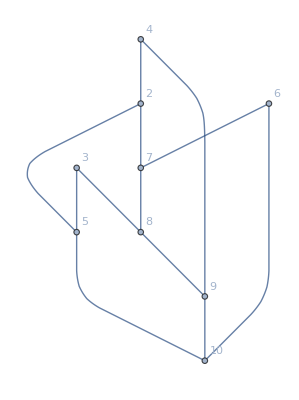

```mathematica
g2=VertexDelete[g,1]
```

```mathematica
Graph[g2,VertexLabels->"Name",GraphLayout->"TutteEmbedding"]
```

```mathematica
ChromaticPolynomial[g2,4]/24
```

329

```mathematica
ChromaticPolynomial[g2,x]//CompleteBaseCoeff
```

{0,0,0,21,308,780,620,192,24,1}

```mathematica
sols2=ToVarsLogical[g2,True]
```

{{x3→1,x4→1,x6→1,x2→2,x5→3,x7→3,x8→2,x9→3,x10→2},{x3→1,x4→1,x6→1,x2→2,x5→3,x7→3,x8→2,x9→3,x10→4},{x3→1,x4→1,x6→1,x2→2,x5→3,x7→3,x8→2,x9→4,x10→2},{x3→1,x4→1,x6→1,x2→2,x5→3,x7→3,x8→4,x9→2,x10→4},{x3→1,x4→1,x6→1,x2→2,x5→3,x7→3,x8→4,x9→3,x10→2},7886,{x3→4,x4→4,x6→4,x2→3,x5→2,x7→2,x8→1,x9→2,x10→3},{x3→4,x4→4,x6→4,x2→3,x5→2,x7→2,x8→1,x9→3,x10→1},{x3→4,x4→4,x6→4,x2→3,x5→2,x7→2,x8→3,x9→1,x10→3},{x3→4,x4→4,x6→4,x2→3,x5→2,x7→2,x8→3,x9→2,x10→1},{x3→4,x4→4,x6→4,x2→3,x5→2,x7→2,x8→3,x9→2,x10→3}}
 |  |  |  |

```mathematica
TableForm[Map[First,Map[SolutionToPartition[#]&,sols2]//Sort//Tally]]
```

01-02-03|04-07-09|05-06-08
01-02-06|03-05-08|04-07-09
01-02-06-09|03-04-07|05-08
01-02-06-09|03-04-08|05-07
01-02-06-09|03-05-07|04-08
01-02-06-09|03-05-08|04-07
01-02-09|03-04-07|05-06-08
01-03-04|02-07-09|05-06-08
01-03-04-08|02-05-06|07-09
01-03-04-08|02-05-07|06-09
01-03-04-08|02-06-09|05-07
01-03-04-08|02-07-09|05-06
01-03-08|02-05-06|04-07-09
01-04-08|02-03-05-07|06-09
01-04-08|02-06-09|03-05-07
01-04-09|02-03-05-07|06-08
01-04-09|02-03-07|05-06-08
01-06-08|02-03-05|04-07-09
01-06-08|02-03-05-07|04-09
01-06-09|02-03-05-07|04-08
01-06-09|02-05-07|03-04-08
01|02-03|04-07-09|05-06-08
01|02-03-05|04-07-09|06-08
01|02-03-05-07|04-08|06-09
01|02-03-05-07|04-09|06-08
01|02-03-07|04-09|05-06-08
01|02-05-06|03-04-08|07-09
01|02-05-06|03-08|04-07-09
01|02-05-07|03-04-08|06-09
01|02-06|03-05-08|04-07-09
01|02-06-09|03-04-07|05-08
01|02-06-09|03-04-08|05-07
01|02-06-09|03-05-07|04-08
01|02-06-09|03-05-08|04-07
01|02-07-09|03-04|05-06-08
01|02-07-09|03-04-08|05-06
01|02-09|03-04-07|05-06-08
01-02|03|04-07-09|05-06-08
01-02|03-04|05-06-08|07-09
01-02|03-04-07|05-06-08|09
01-02|03-04-07|05-08|06-09
01-02|03-04-08|05-06|07-09
01-02|03-04-08|05-07|06-09
01-02|03-05|04-07-09|06-08
01-02|03-05-07|04-08|06-09
01-02|03-05-07|04-09|06-08
01-02|03-05-08|04-07|06-09
01-02|03-05-08|04-07-09|06
01-02|03-07|04-09|05-06-08
01-02|03-08|04-07-09|05-06
01-02-03|04|05-06-08|07-09
01-02-03|04-07|05-06-08|09
01-02-03|04-07|05-08|06-09
01-02-03|04-07-09|05|06-08
01-02-03|04-07-09|05-06|08
01-02-03|04-07-09|05-08|06
01-02-03|04-08|05-06|07-09
01-02-03|04-08|05-07|06-09
01-02-03|04-09|05-06-08|07
01-02-03|04-09|05-07|06-08
01-02-06|03|04-07-09|05-08
01-02-06|03-04|05-08|07-09
01-02-06|03-04-07|05-08|09
01-02-06|03-04-08|05|07-09
01-02-06|03-04-08|05-07|09
01-02-06|03-05|04-07-09|08
01-02-06|03-05|04-08|07-09
01-02-06|03-05-07|04-08|09
01-02-06|03-05-07|04-09|08
01-02-06|03-05-08|04|07-09
01-02-06|03-05-08|04-07|09
01-02-06|03-05-08|04-09|07
01-02-06|03-07|04-09|05-08
01-02-06|03-08|04-07-09|05
01-02-06|03-08|04-09|05-07
01-02-06-09|03|04-07|05-08
01-02-06-09|03|04-08|05-07
01-02-06-09|03-04|05-07|08
01-02-06-09|03-04|05-08|07
01-02-06-09|03-04-07|05|08
01-02-06-09|03-04-08|05|07
01-02-06-09|03-05|04-07|08
01-02-06-09|03-05|04-08|07
01-02-06-09|03-05-07|04|08
01-02-06-09|03-05-08|04|07
01-02-06-09|03-07|04|05-08
01-02-06-09|03-07|04-08|05
01-02-06-09|03-08|04|05-07
01-02-06-09|03-08|04-07|05
01-02-09|03|04-07|05-06-08
01-02-09|03-04|05-06-08|07
01-02-09|03-04|05-07|06-08
01-02-09|03-04-07|05|06-08
01-02-09|03-04-07|05-06|08
01-02-09|03-04-07|05-08|06
01-02-09|03-04-08|05-06|07
01-02-09|03-04-08|05-07|06
01-02-09|03-05|04-07|06-08
01-02-09|03-05-07|04|06-08
01-02-09|03-05-07|04-08|06
01-02-09|03-05-08|04-07|06
01-02-09|03-07|04|05-06-08
01-02-09|03-07|04-08|05-06
01-02-09|03-08|04-07|05-06
01-03|02|04-07-09|05-06-08
01-03|02-05|04-07-09|06-08
01-03|02-05-06|04-07-09|08
01-03|02-05-06|04-08|07-09
01-03|02-05-07|04-08|06-09
01-03|02-05-07|04-09|06-08
01-03|02-06|04-07-09|05-08
01-03|02-06-09|04-07|05-08
01-03|02-06-09|04-08|05-07
01-03|02-07|04-09|05-06-08
01-03|02-07-09|04|05-06-08
01-03|02-07-09|04-08|05-06
01-03|02-09|04-07|05-06-08
01-03-04|02|05-06-08|07-09
01-03-04|02-05|06-08|07-09
01-03-04|02-05-06|07-09|08
01-03-04|02-05-07|06-08|09
01-03-04|02-05-07|06-09|08
01-03-04|02-06|05-08|07-09
01-03-04|02-06-09|05-07|08
01-03-04|02-06-09|05-08|07
01-03-04|02-07|05-06-08|09
01-03-04|02-07|05-08|06-09
01-03-04|02-07-09|05|06-08
01-03-04|02-07-09|05-06|08
01-03-04|02-07-09|05-08|06
01-03-04|02-09|05-06-08|07
01-03-04|02-09|05-07|06-08
01-03-04-08|02|05-06|07-09
01-03-04-08|02|05-07|06-09
01-03-04-08|02-05|06|07-09
01-03-04-08|02-05|06-09|07
01-03-04-08|02-05-06|07|09
01-03-04-08|02-05-07|06|09
01-03-04-08|02-06|05|07-09
01-03-04-08|02-06|05-07|09
01-03-04-08|02-06-09|05|07
01-03-04-08|02-07|05|06-09
01-03-04-08|02-07|05-06|09
01-03-04-08|02-07-09|05|06
01-03-04-08|02-09|05-06|07
01-03-04-08|02-09|05-07|06
01-03-08|02|04-07-09|05-06
01-03-08|02-05|04-07|06-09
01-03-08|02-05|04-07-09|06
01-03-08|02-05-06|04|07-09
01-03-08|02-05-06|04-07|09
01-03-08|02-05-06|04-09|07
01-03-08|02-05-07|04|06-09
01-03-08|02-05-07|04-09|06
01-03-08|02-06|04-07-09|05
01-03-08|02-06|04-09|05-07
01-03-08|02-06-09|04|05-07
01-03-08|02-06-09|04-07|05
01-03-08|02-07|04-09|05-06
01-03-08|02-07-09|04|05-06
01-03-08|02-09|04-07|05-06
01-04|02-03|05-06-08|07-09
01-04|02-03-05|06-08|07-09
01-04|02-03-05-07|06-08|09
01-04|02-03-05-07|06-09|08
01-04|02-03-07|05-06-08|09
01-04|02-03-07|05-08|06-09
01-04|02-05-06|03-08|07-09
01-04|02-05-07|03-08|06-09
01-04|02-06|03-05-08|07-09
01-04|02-06-09|03-05-07|08
01-04|02-06-09|03-05-08|07
01-04|02-06-09|03-07|05-08
01-04|02-06-09|03-08|05-07
01-04|02-07|03-05-08|06-09
01-04|02-07-09|03|05-06-08
01-04|02-07-09|03-05|06-08
01-04|02-07-09|03-05-08|06
01-04|02-07-09|03-08|05-06
01-04|02-09|03-05-07|06-08
01-04|02-09|03-07|05-06-08
01-04-08|02|03-05-07|06-09
01-04-08|02-03|05-06|07-09
01-04-08|02-03|05-07|06-09
01-04-08|02-03-05|06|07-09
01-04-08|02-03-05|06-09|07
01-04-08|02-03-05-07|06|09
01-04-08|02-03-07|05|06-09
01-04-08|02-03-07|05-06|09
01-04-08|02-05|03-07|06-09
01-04-08|02-05-06|03|07-09
01-04-08|02-05-06|03-07|09
01-04-08|02-05-07|03|06-09
01-04-08|02-06|03-05|07-09
01-04-08|02-06|03-05-07|09
01-04-08|02-06-09|03|05-07
01-04-08|02-06-09|03-05|07
01-04-08|02-06-09|03-07|05
01-04-08|02-07|03-05|06-09
01-04-08|02-07-09|03|05-06
01-04-08|02-07-09|03-05|06
01-04-08|02-09|03-05-07|06
01-04-08|02-09|03-07|05-06
01-04-09|02|03-05-07|06-08
01-04-09|02|03-07|05-06-08
01-04-09|02-03|05-06-08|07
01-04-09|02-03|05-07|06-08
01-04-09|02-03-05|06-08|07
01-04-09|02-03-05-07|06|08
01-04-09|02-03-07|05|06-08
01-04-09|02-03-07|05-06|08
01-04-09|02-03-07|05-08|06
01-04-09|02-05|03-07|06-08
01-04-09|02-05-06|03-07|08
01-04-09|02-05-06|03-08|07
01-04-09|02-05-07|03|06-08
01-04-09|02-05-07|03-08|06
01-04-09|02-06|03-05-07|08
01-04-09|02-06|03-05-08|07
01-04-09|02-06|03-07|05-08
01-04-09|02-06|03-08|05-07
01-04-09|02-07|03|05-06-08
01-04-09|02-07|03-05|06-08
01-04-09|02-07|03-05-08|06
01-04-09|02-07|03-08|05-06
01-06|02|03-05-08|04-07-09
01-06|02-03|04-07-09|05-08
01-06|02-03-05|04-07-09|08
01-06|02-03-05|04-08|07-09
01-06|02-03-05-07|04-08|09
01-06|02-03-05-07|04-09|08
01-06|02-03-07|04-09|05-08
01-06|02-05|03-04-08|07-09
01-06|02-05|03-08|04-07-09
01-06|02-05-07|03-04-08|09
01-06|02-05-07|03-08|04-09
01-06|02-07|03-05-08|04-09
01-06|02-07-09|03-04|05-08
01-06|02-07-09|03-04-08|05
01-06|02-07-09|03-05|04-08
01-06|02-07-09|03-05-08|04
01-06|02-09|03-04-07|05-08
01-06|02-09|03-04-08|05-07
01-06|02-09|03-05-07|04-08
01-06|02-09|03-05-08|04-07
01-06-08|02|03-05|04-07-09
01-06-08|02|03-05-07|04-09
01-06-08|02-03|04-07-09|05
01-06-08|02-03|04-09|05-07
01-06-08|02-03-05|04|07-09
01-06-08|02-03-05|04-07|09
01-06-08|02-03-05|04-09|07
01-06-08|02-03-05-07|04|09
01-06-08|02-03-07|04-09|05
01-06-08|02-05|03|04-07-09
01-06-08|02-05|03-04|07-09
01-06-08|02-05|03-04-07|09
01-06-08|02-05|03-07|04-09
01-06-08|02-05-07|03|04-09
01-06-08|02-05-07|03-04|09
01-06-08|02-07|03-05|04-09
01-06-08|02-07-09|03-04|05
01-06-08|02-07-09|03-05|04
01-06-08|02-09|03-04|05-07
01-06-08|02-09|03-04-07|05
01-06-08|02-09|03-05|04-07
01-06-08|02-09|03-05-07|04
01-06-09|02|03-04-07|05-08
01-06-09|02|03-04-08|05-07
01-06-09|02|03-05-07|04-08
01-06-09|02|03-05-08|04-07
01-06-09|02-03|04-07|05-08
01-06-09|02-03|04-08|05-07
01-06-09|02-03-05|04-07|08
01-06-09|02-03-05|04-08|07
01-06-09|02-03-05-07|04|08
01-06-09|02-03-07|04|05-08
01-06-09|02-03-07|04-08|05
01-06-09|02-05|03-04-07|08
01-06-09|02-05|03-04-08|07
01-06-09|02-05|03-07|04-08
01-06-09|02-05|03-08|04-07
01-06-09|02-05-07|03|04-08
01-06-09|02-05-07|03-04|08
01-06-09|02-05-07|03-08|04
01-06-09|02-07|03-04|05-08
01-06-09|02-07|03-04-08|05
01-06-09|02-07|03-05|04-08
01-06-09|02-07|03-05-08|04
01-08|02-03|04-07-09|05-06
01-08|02-03-05|04-07|06-09
01-08|02-03-05|04-07-09|06
01-08|02-03-05-07|04|06-09
01-08|02-03-05-07|04-09|06
01-08|02-03-07|04-09|05-06
01-08|02-05|03-04-07|06-09
01-08|02-05-06|03|04-07-09
01-08|02-05-06|03-04|07-09
01-08|02-05-06|03-04-07|09
01-08|02-05-06|03-07|04-09
01-08|02-05-07|03-04|06-09
01-08|02-06|03-05|04-07-09
01-08|02-06|03-05-07|04-09
01-08|02-06-09|03-04|05-07
01-08|02-06-09|03-04-07|05
01-08|02-06-09|03-05|04-07
01-08|02-06-09|03-05-07|04
01-08|02-07-09|03-04|05-06
01-08|02-09|03-04-07|05-06
01-09|02|03-04-07|05-06-08
01-09|02-03|04-07|05-06-08
01-09|02-03-05|04-07|06-08
01-09|02-03-05-07|04|06-08
01-09|02-03-05-07|04-08|06
01-09|02-03-07|04|05-06-08
01-09|02-03-07|04-08|05-06
01-09|02-05|03-04-07|06-08
01-09|02-05-06|03-04-07|08
01-09|02-05-06|03-04-08|07
01-09|02-05-06|03-07|04-08
01-09|02-05-06|03-08|04-07
01-09|02-05-07|03-04|06-08
01-09|02-05-07|03-04-08|06
01-09|02-06|03-04-07|05-08
01-09|02-06|03-04-08|05-07
01-09|02-06|03-05-07|04-08
01-09|02-06|03-05-08|04-07
01-09|02-07|03-04|05-06-08
01-09|02-07|03-04-08|05-06